```mathematica
SetDirectory[$UserDocumentsDirectory<>"/Github/covidmodel"];
Import["model/autoindent.wl"];
Autoindent["model/model.wl"];
Autoindent["model/data.wl"];
Autoindent["model/gof-metrics.wl"];
```

```mathematica
SetDirectory[$UserDocumentsDirectory<>"/Github/covidmodel"];
Import["model/model.wl"]
```

Fitting model for MA

>> <|chiSquared→0.0000643626,rmsRelativeError→1.11028,rmsRelativeErrorDeaths→1.35172,rmsRelativeErrorPcr→0.888859,meanRelativeErrorDeaths→-0.851743,meanRelativeErrorPcr→-0.504741,rSquaredDeaths→0.0307754,rSquaredPcr→0.0142395,deathResidual7Day→-20.5638,pcrResidual7Day→58.1472|>

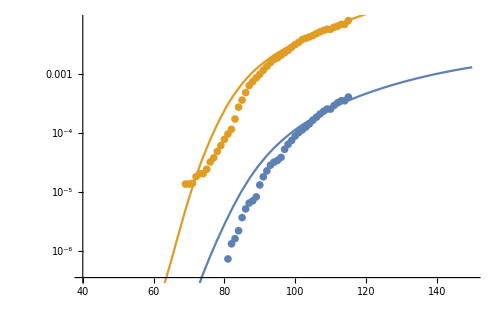
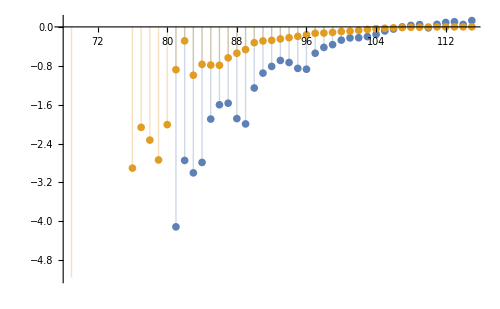
>> Fit for MA
-Graphics--Graphics-
 | Estimate | Standard Error | t-Statistic | P-Value
ⅇ^r0natural | 4.99028 | 0.00552006 | 904.026 | HypothesisTesting`TwoSidedPValue/.HypothesisTesting`StudentTPValue[904.026,78.,HypothesisTesting`TwoSided→True]
ⅇ^importtime | 51.0126 | 0.198786 | 256.621 | HypothesisTesting`TwoSidedPValue/.HypothesisTesting`StudentTPValue[256.621,78.,HypothesisTesting`TwoSided→True]
ⅇ^stateAdjustmentForTestingDifferences | 0.496751 | 0.0688141 | 7.21874 | HypothesisTesting`TwoSidedPValue/.HypothesisTesting`StudentTPValue[7.21874,78.,HypothesisTesting`TwoSided→True]
ⅇ^distpow | 1.45116 | 0.000447592 | 3242.14 | HypothesisTesting`TwoSidedPValue/.HypothesisTesting`StudentTPValue[3242.14,78.,HypothesisTesting`TwoSided→True] | DF | SS | MS
Model | 4 | 1.48586×10^-8 | 3.71466×10^-9
Error | 78 | 1.32441×10^-10 | 1.69796×10^-12
Uncorrected Total | 82 | 1.49911×10^-8 | 
Corrected Total | 81 | 3.47826×10^-9 |

>> Current Indefinite scenario Generating simulations for MA in the

>> Current scenario Generating simulations for MA in the

>> Generating simulations for MA in the  Italy scenario

>> Generating simulations for MA in the  Wuhan scenario

>> Generating simulations for MA in the  Normal scenario

$Aborted

state | distancingLevel | id | distancingDays | maintain | name | gradual | summaryAug1 | totalProjectedDeaths | totalProjectedPCRConfirmed | totalProjectedInfected | totalInfectedFraction | fatalityRate | fatalityRateSymptomatic | fatalityRatePCR | fractionOfSymptomaticHospitalized | fractionOfSymptomaticHospitalizedOrICU | fractionOfPCRHospitalized | fractionOfPCRHospitalizedOrICU | fractionHospitalizedInICU | fractionOfDeathInICU | fractionDeathOfHospitalizedOrICU | fractionOfInfectionsPCRConfirmed | fractionOfDeathsReported | fractionOfHospitalizationsReported | dateContained | dateICUOverCapacity | dateHospitalsOverCapacity | {"r0natural", "importtime", "stateAdjustmentForTestingDifferences", "distpow"} |  |  |  | 
FL | 0.477143 | scenario5 | 613 | True | Current Indefinite | False | <|"totalProjectedDeaths" -> 4154.605507547799, "totalProjectedPCRConfirmed" -> 61287.605800891506, "totalProjectedInfected" -> 251779.80232593007, "totalInfectedFraction" -> 0.01241612843064018, "fatalityRate" -> 0.01650094832535313, "fatalityRateSymptomatic" -> 0.02357278332193305, "fatalityRatePCR" -> 0.06778867363566296, "fractionOfSymptomaticHospitalized" -> 0.08173720154839188, "fractionOfSymptomaticHospitalizedOrICU" -> 0.11719980856887316, "fractionOfPCRHospitalized" -> 0.19756060066316655, "fractionOfPCRHospitalizedOrICU" -> 0.28327449606610927, "fractionHospitalizedInICU" -> 0.302582465394058, "fractionOfDeathInICU" -> 0.7781201344452071, "fractionDeathOfHospitalizedOrICU" -> 0.17564561634851447, "fractionOfInfectionsPCRConfirmed" -> 0.24341748319253356, "fractionOfDeathsReported" -> 0.8447542936110652, "fractionOfHospitalizationsReported" -> 0.8404933875263647, "dateContained" -> "Tue 27 Oct 2020 17:25:08", "dateICUOverCapacity" -> "", "dateHospitalsOverCapacity" -> ""|> | 4474.93 | 65366.1 | 262601. | 0.0129497 | 0.0170408 | 0.024344 | 0.0684595 | 0.083015 | 0.119032 | 0.196293 | 0.281457 | 0.302582 | 0.779553 | 0.175646 | 0.248918 | 0.844879 | 0.840829 | Tue 27 Oct 2020 17:25:08 |  |  | 3.99195 | 48.1684 | 1.31006 | 2.12463 | 
FL | 0.477143 | scenario1 | 90 | True | Current | False | <|"totalProjectedDeaths" -> 4154.623616962053, "totalProjectedPCRConfirmed" -> 61340.815232362336, "totalProjectedInfected" -> 252768.4990076893, "totalInfectedFraction" -> 0.012464884466137338, "fatalityRate" -> 0.01643647698693526, "fatalityRateSymptomatic" -> 0.023480681409907517, "fatalityRatePCR" -> 0.06773016630483494, "fractionOfSymptomaticHospitalized" -> 0.081422953695138, "fractionOfSymptomaticHospitalizedOrICU" -> 0.11674922073925766, "fractionOfPCRHospitalized" -> 0.19740257240585443, "fractionOfPCRHospitalizedOrICU" -> 0.28304790546654623, "fractionHospitalizedInICU" -> 0.3025824653940579, "fractionOfDeathInICU" -> 0.778119615754711, "fractionDeathOfHospitalizedOrICU" -> 0.17564561634851447, "fractionOfInfectionsPCRConfirmed" -> 0.2426758693158847, "fractionOfDeathsReported" -> 0.8447543011799923, "fractionOfHospitalizationsReported" -> 0.8404937900496152, "dateContained" -> "", "dateICUOverCapacity" -> "Mon 31 Aug 2020 08:49:15", "dateHospitalsOverCapacity" -> "Wed 2 Sep 2020 03:23:05"|> | 245843. | 4.66975×10^6 | 1.43555×10^7 | 0.707918 | 0.0171254 | 0.0244648 | 0.0526457 | 0.0832148 | 0.119318 | 0.151562 | 0.217319 | 0.302582 | 0.779527 | 0.175646 | 0.325294 | 0.846461 | 0.846387 |  | Mon 31 Aug 2020 08:49:15 | Wed 2 Sep 2020 03:23:05 | 3.99195 | 48.1684 | 1.31006 | 2.12463 | 
FL | 0.2 | scenario2 | 90 | False | Italy | False | <|"totalProjectedDeaths" -> 2639.908381444287, "totalProjectedPCRConfirmed" -> 37182.83523824069, "totalProjectedInfected" -> 172839.3031727327, "totalInfectedFraction" -> 0.008523300781994435, "fatalityRate" -> 0.01527377357455559, "fatalityRateSymptomatic" -> 0.021819676535079414, "fatalityRatePCR" -> 0.07099803886738774, "fractionOfSymptomaticHospitalized" -> 0.08068506072628084, "fractionOfSymptomaticHospitalizedOrICU" -> 0.11569118458122776, "fractionOfPCRHospitalized" -> 0.2199119052119376, "fractionOfPCRHospitalizedOrICU" -> 0.31532316625247053, "fractionHospitalizedInICU" -> 0.3025824653940578, "fractionOfDeathInICU" -> 0.7715037059019951, "fractionDeathOfHospitalizedOrICU" -> 0.17564561634851444, "fractionOfInfectionsPCRConfirmed" -> 0.21512951369099642, "fractionOfDeathsReported" -> 0.8437579743573357, "fractionOfHospitalizationsReported" -> 0.8376403051790181, "dateContained" -> "Thu 21 May 2020 20:07:53", "dateICUOverCapacity" -> "Sun 11 Oct 2020 19:14:35", "dateHospitalsOverCapacity" -> "Tue 13 Oct 2020 12:44:53"|> | 2639.91 | 37182.8 | 172839. | 0.0085233 | 0.0152738 | 0.0218197 | 0.070998 | 0.0806851 | 0.115691 | 0.219912 | 0.315323 | 0.302582 | 0.771504 | 0.175646 | 0.21513 | 0.843758 | 0.83764 | Thu 21 May 2020 20:07:53 | Sun 11 Oct 2020 19:14:35 | Tue 13 Oct 2020 12:44:53 | 3.99195 | 48.1684 | 1.31006 | 2.12463 | 
FL | 0.11 | scenario3 | 60 | False | Wuhan | False | <|"totalProjectedDeaths" -> 2315.8822100185025, "totalProjectedPCRConfirmed" -> 35734.38277948275, "totalProjectedInfected" -> 169802.33748232888, "totalInfectedFraction" -> 0.00837353755355767, "fatalityRate" -> 0.013638694521855527, "fatalityRateSymptomatic" -> 0.01948384931693647, "fatalityRatePCR" -> 0.06480823313249415, "fractionOfSymptomaticHospitalized" -> 0.07730242863374319, "fractionOfSymptomaticHospitalizedOrICU" -> 0.11084095939374529, "fractionOfPCRHospitalized" -> 0.21523830961786844, "fractionOfPCRHospitalizedOrICU" -> 0.30862187848414696, "fractionHospitalizedInICU" -> 0.3025824653940578, "fractionOfDeathInICU" -> 0.7651596709246268, "fractionDeathOfHospitalizedOrICU" -> 0.17564561634851444, "fractionOfInfectionsPCRConfirmed" -> 0.2104469426588523, "fractionOfDeathsReported" -> 0.8433756199180231, "fractionOfHospitalizationsReported" -> 0.8370878047746773, "dateContained" -> "Tue 12 May 2020 03:27:29", "dateICUOverCapacity" -> "Tue 1 Sep 2020 19:10:48", "dateHospitalsOverCapacity" -> "Thu 3 Sep 2020 12:38:58"|> | 2315.88 | 35734.4 | 169802. | 0.00837354 | 0.0136387 | 0.0194838 | 0.0648082 | 0.0773024 | 0.110841 | 0.215238 | 0.308622 | 0.302582 | 0.76516 | 0.175646 | 0.210447 | 0.843376 | 0.837088 | Tue 12 May 2020 03:27:29 | Tue 1 Sep 2020 19:10:48 | Thu 3 Sep 2020 12:38:58 | 3.99195 | 48.1684 | 1.31006 | 2.12463 | 
FL | 1 | scenario4 | 90 | False | Normal | False | <|"totalProjectedDeaths" -> 234940.01411986875, "totalProjectedPCRConfirmed" -> 4.525447511176455*^6, "totalProjectedInfected" -> 1.4354587285621978*^7, "totalInfectedFraction" -> 0.7078740933968947, "fatalityRate" -> 0.016366894390282632, "fatalityRateSymptomatic" -> 0.023381277700403765, "fatalityRatePCR" -> 0.051915310815038654, "fractionOfSymptomaticHospitalized" -> 0.08221517779164272, "fractionOfSymptomaticHospitalizedOrICU" -> 0.1178851601976086, "fractionOfPCRHospitalized" -> 0.15450686165377014, "fractionOfPCRHospitalizedOrICU" -> 0.22154140667121347, "fractionHospitalizedInICU" -> 0.3025824653940578, "fractionOfDeathInICU" -> 0.7760273176902678, "fractionDeathOfHospitalizedOrICU" -> 0.17564561634851444, "fractionOfInfectionsPCRConfirmed" -> 0.31526141581996514, "fractionOfDeathsReported" -> 0.8464600340008477, "fractionOfHospitalizationsReported" -> 0.8463861586362793, "dateContained" -> "", "dateICUOverCapacity" -> "Sat 23 May 2020 15:30:37", "dateHospitalsOverCapacity" -> "Mon 25 May 2020 11:24:13"|> | 246447. | 4.55476×10^6 | 1.43908×10^7 | 0.709659 | 0.0171254 | 0.0244648 | 0.0541077 | 0.0832148 | 0.119318 | 0.155771 | 0.223354 | 0.302582 | 0.779527 | 0.175646 | 0.316505 | 0.846461 | 0.846388 |  | Sat 23 May 2020 15:30:37 | Mon 25 May 2020 11:24:13 | 3.99195 | 48.1684 | 1.31006 | 2.12463 | 
FL | 0.477143 | scenario6 | 5 | True | 1 | Open May 1 | False | <|"totalProjectedDeaths" -> 228963.47173308244, "totalProjectedPCRConfirmed" -> 4.553046296958006*^6, "totalProjectedInfected" -> 1.4326528535078174*^7, "totalInfectedFraction" -> 0.7064904198570124, "fatalityRate" -> 0.015981783107643324, "fatalityRateSymptomatic" -> 0.02283111872520475, "fatalityRatePCR" -> 0.050287973545548655, "fractionOfSymptomaticHospitalized" -> 0.08161955156859278, "fractionOfSymptomaticHospitalizedOrICU" -> 0.11703111481805488, "fractionOfPCRHospitalized" -> 0.15215954543111176, "fractionOfPCRHospitalizedOrICU" -> 0.21817568082380612, "fractionHospitalizedInICU" -> 0.30258246539405775, "fractionOfDeathInICU" -> 0.7743756852596523, "fractionDeathOfHospitalizedOrICU" -> 0.17564561634851442, "fractionOfInfectionsPCRConfirmed" -> 0.3178052719338098, "fractionOfDeathsReported" -> 0.8464592324738036, "fractionOfHospitalizationsReported" -> 0.8463851891176942, "dateContained" -> "", "dateICUOverCapacity" -> "Fri 29 May 2020 04:35:02", "dateHospitalsOverCapacity" -> "Sun 31 May 2020 00:18:26"|> | 246375. | 4.60088×10^6 | 1.43866×10^7 | 0.709451 | 0.0171254 | 0.0244648 | 0.0535496 | 0.0832148 | 0.119318 | 0.154165 | 0.221051 | 0.302582 | 0.779527 | 0.175646 | 0.319804 | 0.846461 | 0.846388 |  | Fri 29 May 2020 04:35:02 | Sun 31 May 2020 00:18:26 | 3.99195 | 48.1684 | 1.31006 | 2.12463
FL | 0.477143 | scenario7 | 60 | True | 1 | Open Gradual May 1 | True | <|"totalProjectedDeaths" -> 141864.5416993249, "totalProjectedPCRConfirmed" -> 4.1022135595340077*^6, "totalProjectedInfected" -> 1.3488772287787188*^7, "totalInfectedFraction" -> 0.6651777765717063, "fatalityRate" -> 0.010517231566565172, "fatalityRateSymptomatic" -> 0.015024616523664531, "fatalityRatePCR" -> 0.03458243693081645, "fractionOfSymptomaticHospitalized" -> 0.0690431087842289, "fractionOfSymptomaticHospitalizedOrICU" -> 0.09899824044894415, "fractionOfPCRHospitalized" -> 0.13450138244814133, "fractionOfPCRHospitalizedOrICU" -> 0.19285632461784585, "fractionHospitalizedInICU" -> 0.30258246539405786, "fractionOfDeathInICU" -> 0.7503135878282453, "fractionDeathOfHospitalizedOrICU" -> 0.1756456163485145, "fractionOfInfectionsPCRConfirmed" -> 0.30412060282522346, "fractionOfDeathsReported" -> 0.8464398876789732, "fractionOfHospitalizationsReported" -> 0.8463582128250673, "dateContained" -> "", "dateICUOverCapacity" -> "Wed 24 Jun 2020 07:47:18", "dateHospitalsOverCapacity" -> "Sat 27 Jun 2020 04:05:25"|> | 244875. | 4.64403×10^6 | 1.4299×10^7 | 0.705132 | 0.0171254 | 0.0244648 | 0.0527291 | 0.0832148 | 0.119318 | 0.151802 | 0.217663 | 0.302582 | 0.779527 | 0.175646 | 0.32478 | 0.846461 | 0.846387 |  | Wed 24 Jun 2020 07:47:18 | Sat 27 Jun 2020 04:05:25 | 3.99195 | 48.1684 | 1.31006 | 2.12463

```mathematica
asd=GenerateModelExport[10,{"CA"}];
TableForm[Import["tests/summary.csv"]]
```

```mathematica
100CDF[NormalDistribution[1,.05],0]
```

2.75362×10^-87